```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Subscript[η, B]=Last[Flatten[StringSplit[FileNames["ETAB_*",NotebookDirectory[]],"_"]]];
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];
```

/homes/ht/Desktop/analytical_prakash_kappa6/Analysis_1.0

```mathematica
DataPointsFc1=Import["old_force.data","Table"];
DataPointsFc2=Import["new_force.data","Table"];
DataPointsFc3=Import["new2_force.data","Table"];
```

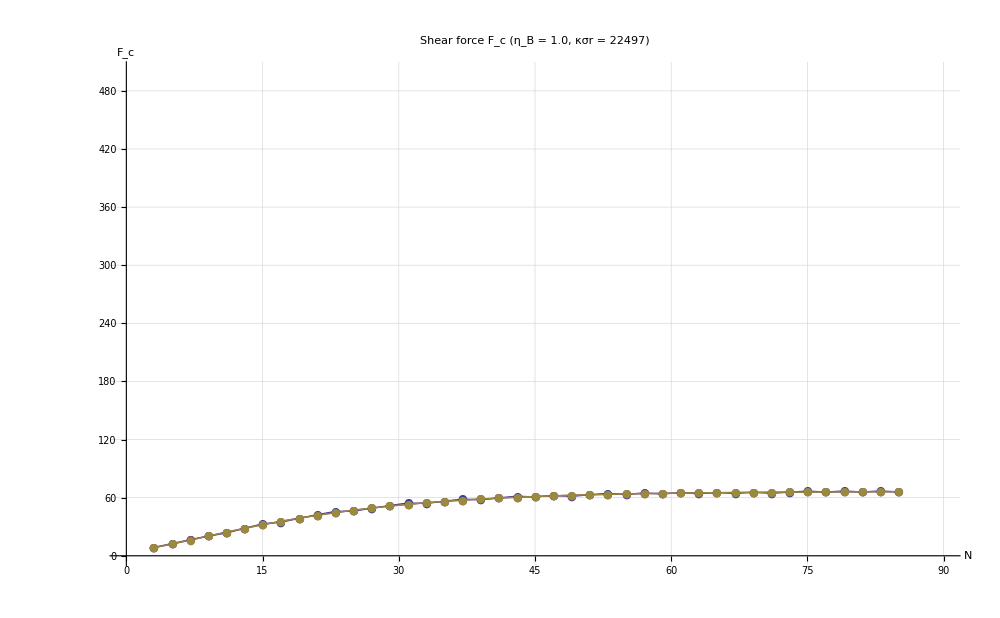

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

Data=ListLinePlot[{DataPointsFc1,DataPointsFc2,DataPointsFc3},PlotMarkers->{"●"}];

Show[
{
Data
},
PlotRange->{{0,90},{0,500}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[Subscript[η, B]]<>", κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->1000
]
```